# Learning XOR

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## Get data

```mathematica
numBooleanVariables=10; (* 2^numBooleanVariables possible inputs *)
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=200;
numClasses=2;
examples=Dataset[Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Association[{"Input"->Soften/@x,"Target"->With[{r=bf@@x},r]}]]&,Range[maxExamples]]]
```

```mathematica
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
targetEncoder=NetEncoder[{"Class",{True,False},"IndicatorVector"}];
```

## Create net

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=8*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,50],
HardDropoutLayer[0.25],
HardNeuralMajority[50,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
trainableSoftNet=NetGraph[<|"NeuralLogicNet"->softNet,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"},"Target"->targetEncoder];
```

```mathematica
trainableSoftNet
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableSoftNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,{},
"Output"->NetDecoder[targetEncoder]]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]
]};
```

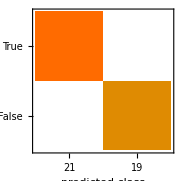
{Classifier Measurements
Classifier method | Net
Number of test examples | 40
Accuracy | (100.00000000000000022) %
Accuracy baseline | (53.8.) %
Geometric mean of probabilities | 0.965 ± 0.009
Mean cross entropy | 0.0352 ± 0.0093
Single evaluation time | 3.05 ms/example
Batch evaluation speed | 460. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 40
Accuracy | (100.00000000000000022) %
Accuracy baseline | (53.8.) %
Geometric mean of probabilities | 0.965 ± 0.009
Mean cross entropy | 0.0352 ± 0.0093
Single evaluation time | 3.42 ms/example
Batch evaluation speed | 925. examples/s
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Target"]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
targetEncoder[True]
```

{1,0}

```mathematica
targetEncoder[False]
```

{0,1}

```mathematica
NetDecoder[targetEncoder][{0,1}]
```

False

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[targetEncoder]]
```

{<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→True,Target→False|>,<|Prediction→False,Target→True|>}

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

0.

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[KeyDrop[{"Target"}]@#],"Target"->#["Target"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

1.

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

0.158691 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Acceptability",Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

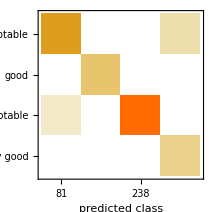
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 346
Accuracy | (99.10.5) %
Accuracy baseline | (69.12.5) %
Geometric mean of probabilities | 0.956 ± 0.03
Mean cross entropy | 0.0445 ± 0.032
Single evaluation time | 7.04 ms/example
Batch evaluation speed | 1.43 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Acceptability"]
```

```mathematica
Information[classifier,"FunctionMemory"]
```

753. kB

## Notes

```mathematica
softWeights=Flatten[ExtractWeights[trainedSoftNet]];
```

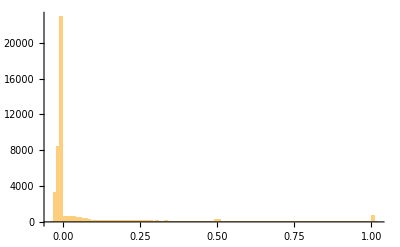

```mathematica
Histogram[softWeights,PlotRange->All]
```